```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{-1,-1},{1,0},{2,1},{4,2},{5,3},{7,4}}

{{-2,-1},{0,0},{1,1},{3,2},{4,3},{6,4}}

{{-2,-1},{0,0},{1,1},{3,2},{4,3},{6,4}}

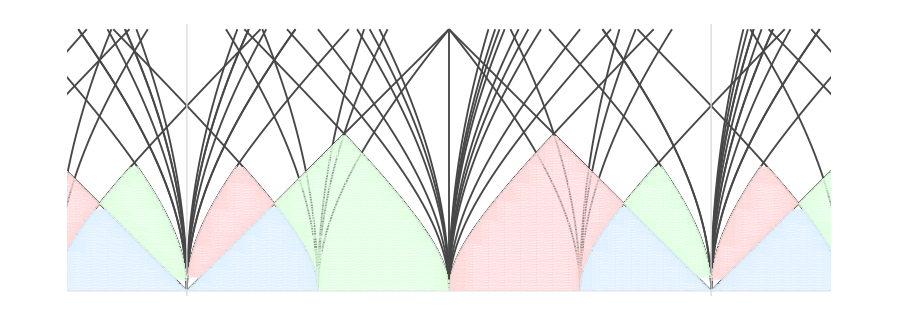

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=0, psi=0, xmin=-1, xmax=2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Echo@ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

plt1=Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->Directive[RGBColor[0.28, 0.28, 0.28],Thickness[.0015]],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

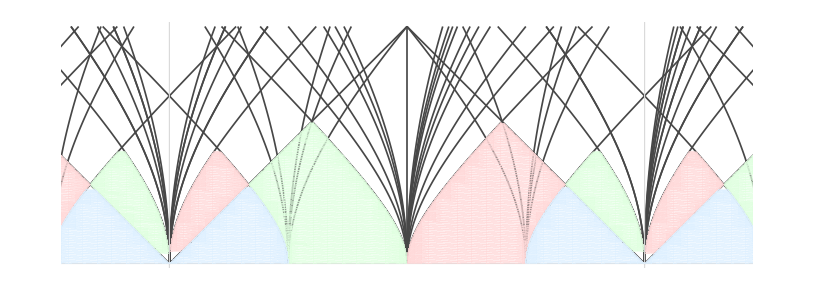

```mathematica
Show[plt1,
ContourPlot[2-8 s+8 s^2+8 t^2==0,{s,-.2,1.2},{t,0,1}]]
```

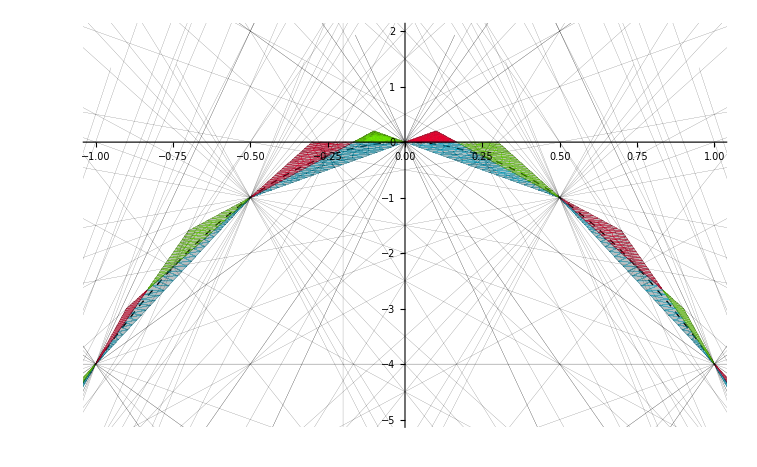

```mathematica
plotData={
<|"coll"->CollBridgeland, "mB"->Function[{m,mu},(2m+3mu-1)/3], "color"->RGBColor[0, 0.8260000000000001, 1]|>,
<|"coll"->CollArcaraI, "mB"->Function[{m,mu},(2m+3mu-3)/3], "color"->RGBColor[0.46900000000000003, 1, 0]|>,
<|"coll"->CollArcaraII, "mB"->Function[{m,mu},(2m+3mu-1)/3], "color"->RGBColor[1, 0, 0.192]|>
};
With[{mu=0, L=4, Lp=6,len=20},
constructDomain[asc_]:=Module[{ineq},
ineq=Table[
If[IntegerQ[asc["mB"][mF,mu]],Nothing,
CollInequalities[SpectralFlow[asc["coll"]/.repCh, {mF,Ceiling[asc["mB"][mF,mu]]}],{x,y},mu]], {mF, -L,L}];
{EdgeForm[Opacity[.25,asc["color"]]], DiscretizeRegion[ImplicitRegion[And@@#,{x,y}]]&/@ineq}
];
rays=Flatten[Table[{#, InitialPositionXY[#, mu],0,0,0,0,0}&[s Ch[p,q]/.repCh], {p,-Lp,Lp},{q,-Lp,Lp},{s,{-1,1}}], 2];

Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-5,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
Graphics[{Opacity[.25],constructDomain/@plotData}],
Graphics[{
Tooltip[XYRaySegment[#,mu,len,<||>,Directive[Thickness[.0001],Black]], #[[1]]]&/@rays
}]
]
]
```

```mathematica
{Ch[1,0],Ch[1,1],Ch[2,1],Ch[2,2]}/.repCh
XYRay[#,{x,y},0]&/@%
%/.{x->1/2,y->-1}
```

{{1,1,0,0},{1,1,1,1/2},{1,2,1,3/2},{1,2,2,2}}

{2 x+y,-1/2+3 x+y,-3/2+5 x+y,-2+6 x+y}

{0,0,0,0}

```mathematica
Coll0={Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1],Ch[2,2]};
initRays=InitialRaysFromColl[Coll0/.repCh,-2,2,0];
```

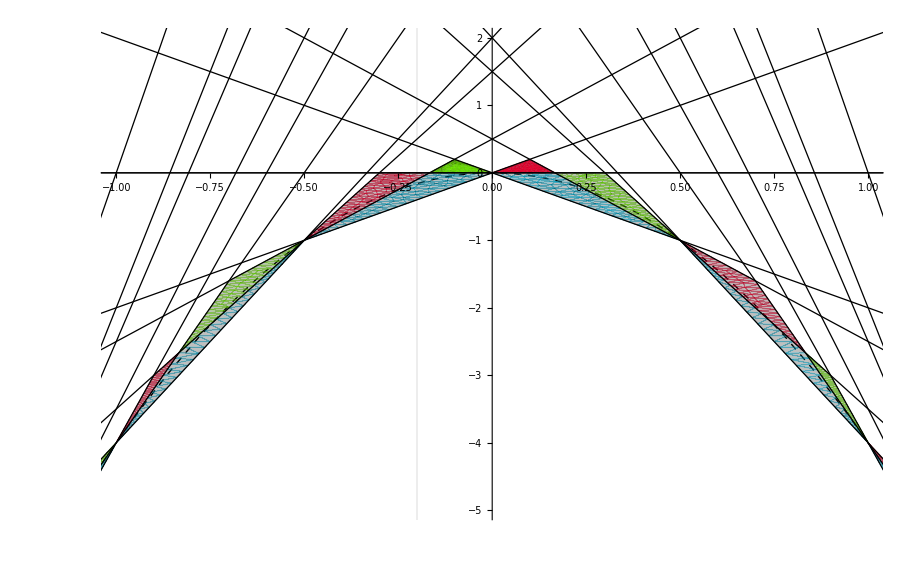

```mathematica
plotData={
<|"coll"->CollBridgeland, "mB"->Function[{m,mu},(2m+3mu-1)/3], "color"->RGBColor[0, 0.8260000000000001, 1]|>,
<|"coll"->CollArcaraI, "mB"->Function[{m,mu},(2m+3mu-3)/3], "color"->RGBColor[0.46900000000000003, 1, 0]|>,
<|"coll"->CollArcaraII, "mB"->Function[{m,mu},(2m+3mu-1)/3], "color"->RGBColor[1, 0, 0.192]|>
};
With[{mu=0, L=4, Lp=6,len=20,rays=initRays},
constructDomain[asc_]:=Module[{ineq},
ineq=Table[
If[IntegerQ[asc["mB"][mF,mu]],Nothing,
CollInequalities[SpectralFlow[asc["coll"]/.repCh, {mF,Ceiling[asc["mB"][mF,mu]]}],{x,y},mu]], {mF, -L,L}];
{EdgeForm[Opacity[.25,asc["color"]]], DiscretizeRegion[ImplicitRegion[And@@#,{x,y}]]&/@ineq}
];
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-5,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None},
PlotHighlighting->None
],
Graphics[{Opacity[.25],constructDomain/@plotData}],
Graphics[{
Tooltip[XYRaySegment[#,mu,len,<||>,Directive[Thickness[.001],Black]], #[[1]]]&/@rays
}]
]
]
```

```mathematica
DSZ@@{-Ch[1,0],Ch[0,0]}/.repCh
```

2

```mathematica
Select[#.{-Ch[1,0],Ch[0,0]}&/@KroneckerDims[2,20]/.repCh,Abs[#[[1]]]<=1&]
```

{{0,-1,0,0},{1,-1,0,0},{-1,-2,0,0},{1,-2,0,0},{-1,-3,0,0},{1,-3,0,0},{-1,-4,0,0},{1,-4,0,0},{-1,-5,0,0},{1,-5,0,0},{-1,-6,0,0},{1,-6,0,0},{-1,-7,0,0},{1,-7,0,0},{-1,-8,0,0},{1,-8,0,0},{-1,-9,0,0},{1,-9,0,0},{-1,-10,0,0}}

```mathematica
DSZ@@{-Ch[-1,0],Ch[1,0]}/.repCh
```

-4

```mathematica
Select[#.{-Ch[-1,0],Ch[1,0]}&/@KroneckerDims[4,20]/.repCh,Abs[#[[1]]]<=1&]
```

{{0,2,0,0},{1,3,0,0},{-1,3,0,0},{1,5,0,0},{-1,5,0,0},{1,7,0,0},{-1,7,0,0},{1,9,0,0},{-1,9,0,0},{1,11,0,0},{-1,11,0,0},{1,13,0,0},{-1,13,0,0},{1,15,0,0},{-1,15,0,0},{1,17,0,0},{-1,17,0,0},{1,19,0,0},{-1,19,0,0}}

## Walls at m=0

```mathematica
circleParams[expr_,{x_,y_}]:=Module[{Q,b,F},
Q = 1/2D[expr,{{x,y},2}];
b = 1/2D[expr,{{x,y}}]/.{x->0,y->0};
F = expr/.{x->0,y->0};
{-Inverse[Q].b,2(b.Inverse[Q].b-F)/Tr[Q]}
]
circleParams[-60-24 x+4 x^2+8 y+4 y^2,{x,y}]
```

{{3,-1},25}

```mathematica
chargesAtHalf={Ch[1,0],Ch[1,1],Ch[2,1],Ch[2,2]};
combinations = Subsets[%, {2}]
```

{{Ch[1,0],Ch[1,1]},{Ch[1,0],Ch[2,1]},{Ch[1,0],Ch[2,2]},{Ch[1,1],Ch[2,1]},{Ch[1,1],Ch[2,2]},{Ch[2,1],Ch[2,2]}}

```mathematica
combinations[[3]]
With[{g1=%[[1]]/.repCh,g2=%[[2]]/.repCh,T=s+I t}, Module[{wallexpr},
Print["DSZ=",DSZ[g1,g2]];
wallexpr = Simplify[ComplexExpand[Im[ZLV[g1,T,m]**ZLV[g2,T,m]], {T}]];
Print[wallexpr];
Simplify[circleParams[Last[wallexpr],{s,t}]]
]]
```

{Ch[1,0],Ch[2,2]}

DSZ=4

t (m^2+m (4-8 s)+4 (1-4 s+4 s^2+4 t^2))

{{(2+m)/4,0},0}

At m = 0, wall is at a single point (s, t) = (1/2, 0)